# Numerical Solution for Functional Square Roots

## Input

Input a function and a finite range over which the solution will be found. The step size indicates the distance between the points where error is calculated.

```mathematica
f[x_]:=Sin[x]+LogisticSigmoid[x];
originalRange={-2*Pi,2*Pi,0.3};
range=originalRange;
```

Here is a plot of the inputted function over the range:

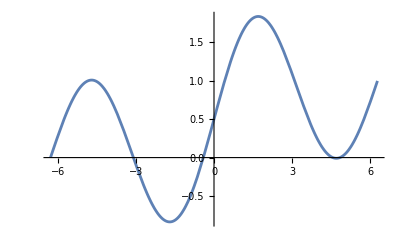

```mathematica
pRange=AbsoluteOptions[Plot[f[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
pRange[[2,1]]=Min[0,pRange[[2,1]]]; (* Set the plotting range manually *)

Plot[f[x],{x, range[[1]], range[[2]]}, PlotRange->pRange]
```

## Helper Functions

As many operations in this notebook take a very long time to run, this function gives an progress indicator for them:

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[{progress=PrintTemporary["0% "<>message]}, Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message]; func[l[[i]]],{i, Length[l]}]]
```

Makes a linear spline between points (i.e. connects them with straight lines), and extends the domain using the last two points on either end.

```mathematica
LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
```

## Method 1: Exact Nested Solution from Initial X and W

## Explanation

We are trying to solve the equation g(g(x)) = f(x) for all x.
Given an initial x, xi, we can make a guess as to the value of g:
g(xi) = w
Because we know that g(g(x)) = f(x), then g(g(xi)) = f(xi), and since g(xi) = w, then:
g(w) = f(xi)
This gives a second value of g. For a third, we can repeat the same thing. g(g(x)) = f(x), so g(g(w)) = f(w), and since g(w) = f(xi):
g(f(xi)) = f(w)
If you continue this, you get as many points as you want that will all lie on the g, assuming that g(xi) = w. By searching over all xi and all w, we can find the solution which minimizes the squared difference between a linear spline of the approximating points and the original function.

This is a function which more efficiently implements the process described above:

```mathematica
approximatingPoints[xii_,w_,n_:20]:=Join[Transpose[{NestList[f, xii, n], NestList[f, w, n]}],Transpose[{NestList[f, w, n], NestList[f, f[xii], n]}]]
```

FInally, here are more helper functions relating to it, which are fairly self-explanatory.

```mathematica
approxFunc[xii_, w_]:=LinearSpline[approximatingPoints[xii, w]]
error[af_]:=Quiet[Sum[(af[af[x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}],General::munfl]
errorFunc[xii_, w_]:=error[approxFunc[xii,w]]
```

## Search

For every xii and w, the Search[] function checks the error of it, setting minP to be the values of xii and w which minimize error, and returning that minimum error. By then subdividing the region around minP, a better and better solution can be found. As the first iteration is the biggest search (in order to minimize the effect of local minima), it takes much longer than all other iterations.

```mathematica
(* Tweak the last value of each of these for faster first-step evaluation times. *)
xiiRange=range;wRange=range; 

search[anything___]:=(
points=ParallelTable[errorFunc[xii, w],{xii, xiiRange[[1]],  xiiRange[[2]],  xiiRange[[3]]}, {w, wRange[[1]],  wRange[[2]],  wRange[[3]]}];
minI=First[Position[points,Min[points],2]];
minP={xiiRange[[1]]+minI[[1]]xiiRange[[3]], wRange[[1]]+minI[[2]]wRange[[3]]};
minV=errorFunc@@minP;

xiiRange={minP[[1]]-xiiRange[[3]], minP[[1]]+xiiRange[[3]], 0.5xiiRange[[3]]};
wRange={minP[[2]]-wRange[[3]], minP[[2]]+ wRange[[3]], 0.5wRange[[3]]};

minV
);
```

```mathematica
PrintTemporary["The first step takes way longer than future steps"];
progressMap[search,Range[20]]
```

{485488.,1843.85,52.0278,15.6268,11.6272,10.6174,10.2497,10.092,10.0189,9.98376,9.9665,9.95795,9.9537,9.95158,9.95052,9.94999,9.94972,9.94959,9.94952,9.94949}

## Output

Based on the search, here is the best function found so far:

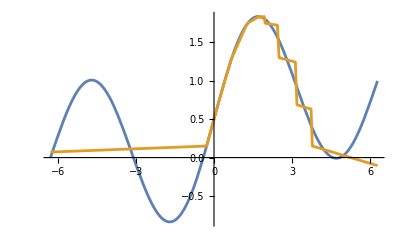

```mathematica
aFunc= approxFunc@@minP;
Plot[{f[x], aFunc[aFunc[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```

And here are the xii and w values, and the error which were achieved:

```mathematica
minP
minV
```

{4.21682,-0.283185}

9.94949

## Method 2: Whole-Domain Numerical Minimization

## Explanation

Instead of being smart about nesting functions with a single initial guess, this method tries to determine the whole function at once in order to move the values closer to what is needed. It is extremely susceptible to local minima, but it can often do a much better job of optimizing simpler functions, such as sine or some polynomials.

First, take a guess at a functional root g. I’ve used the g from method 1 here, but you could probably use almost anything. Next, find the differences between that and the original function:
delta(x) = f(x) - g(g(x))

Finally, simply add the delta vals to g:
new_g(x) = g(x) + temperature * delta(x)

For some points, g(x) will not be affected much, but g(g(x)) will be moved closer to f. In this case, g will be positively affected. For other points, it may shoot off to infinity or become discontinuous, so there is no real guarantee that this will work.

## Implementation

First, it represents both the original function and the approximation as a set of points, with xVals being the x values of the points, fVals being the corresponding y values of the original function, and aVals being the approximated y values.

```mathematica
range[[3]]=originalRange[[3]]/5;

aFunc= approxFunc@@minP;
xVals=Range@@range;
fVals=f/@xVals;
aVals=aFunc[aFunc[#]]&/@xVals;

(* Generates the interpolating function from a list of y values *)
funcFromVals[vals_]:=LinearSpline[Transpose[{xVals,  vals}]]
```

Here are plots of the interpolated values for the original function and the function from method 1:

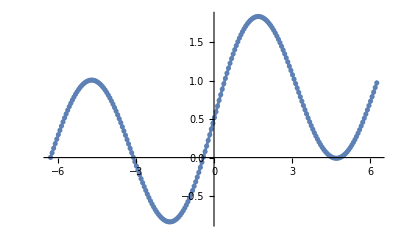

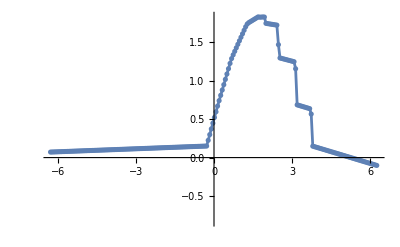

```mathematica
PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange->pRange], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}, PlotRange->pRange]}]
PlotVals[fVals]
PlotVals[aVals]
```

## Optimization

This repeatedly applies the method described to optimize the function.

```mathematica
aValsHist={aVals};
progressMap[
(aFunc=funcFromVals[aVals];
aVals=aVals+0.3*(fVals-ParallelMap[aFunc[aFunc[#]]&,xVals]);
AppendTo[aValsHist, aVals];)&,Range[50] , "Optimized"];

(* Find the optimization which actually minimized error *)
bestVals=aValsHist[[First[PositionSmallest[ParallelMap[error[funcFromVals[#]]&,aValsHist]]]]];
aFunc=funcFromVals[bestVals];
```

Plot the progress made so far:

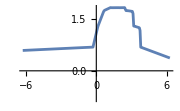
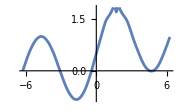
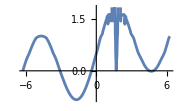
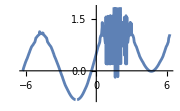
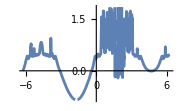

```mathematica
ParallelMap[With[{aFunc=funcFromVals[aValsHist[[#]]]},Plot[aFunc[aFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Small, PlotRange->pRange]]&, Round/@Subdivide[1, Length[aValsHist], 4]]
```

## Output

Plot the original and the best output:

-Graphics-

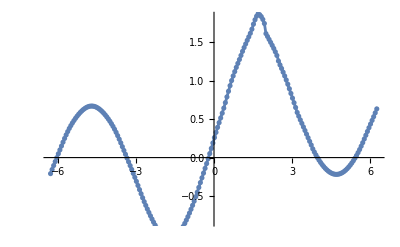

```mathematica
PlotVals[fVals]
PlotVals[bestVals]
```

## Final Approximation

```mathematica
"Method 1 Error:"
e1=error[approxFunc@@minP]
"Method 2 Error:"
e2=error[aFunc]

(* Choose the one with the least error *)
approximation=If[e1<e2,approxFunc@@minP, aFunc];
```

Method 1 Error:

52.0495

Method 2 Error:

0.0389273

A plot of the final approximation:

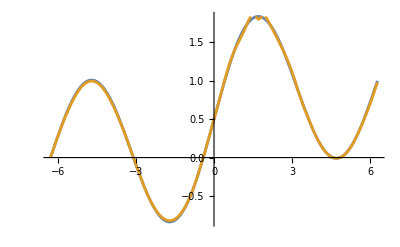

```mathematica
Plot[{f[x], approximation[approximation[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```